```mathematica
clear[r, Equation]
r [ θ_, n_] :=Sec[θ-Floor[θ*n/(2*π)]*2π/n-π/n]
N[r[2, 4]]
```

clear[r,Equation]

1.06697

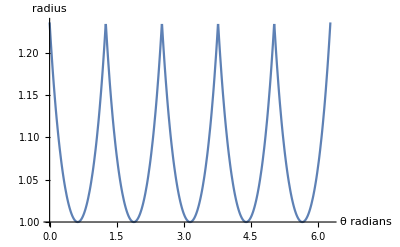

```mathematica
Plot[r[θ, 5], {θ, 0,2*π}, AxesLabel->{θ(radians), radius}]
```

```mathematica
f[x_] := Sin[x]+Sin[3*x]
ft[n_]:=Abs[FourierCoefficient[r[θ, 4], θ, n]]
fto[n_] := Abs[FourierCoefficient[Sin[θ]+Sin[3*θ], θ, n]]
 DiscretePlot[ft[n], {n, 1, 11}]
```

$Aborted

```mathematica
NFourierTransform[r[θ, 4], θ, t]
```

```mathematica
NFourierTransform[Sec[π/4-θ+1/2 π Floor[(2 θ)/π]],θ,t]
```

NFourierTransform[Sec[π/4-θ+1/2 π Floor[(2 θ)/π]],θ,t]

```mathematica
FourierSequenceTransform[r[t,4],t,x]
```

FourierSequenceTransform[Sec[0.7854-1. t+1.5708 Floor[0.63662 t]],t,x]

```mathematica
1/(2 π) Integrate[r[t,4]* E^(-3 I t),{t,-π,π}]
```

(∫_-π^π ⅇ^(-3 ⅈ t) Sec[0.7854-1. t+1.5708 Floor[0.63662 t]]ⅆt)/(2 π)

```mathematica
PolarPlot[r[θ,5],{θ,0, 2*π},PolarAxes->Automatic,PolarTicks->{"Degrees",Automatic}]
```

-Graphics-

```mathematica
FourierSequenceTransform[r[θ, 4], θ, 4]
```

```mathematica
FourierSequenceTransform[Sec[π/4-θ+1/2 π Floor[(2 θ)/π]],θ,4]
```

0.753544

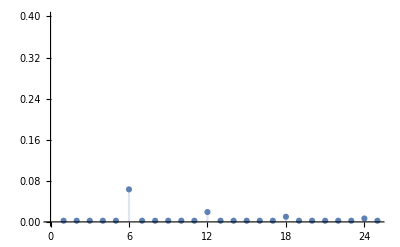

```mathematica
clear[a, Equation];
clear[b, Equation];
clear[c, Equation];
a[s_, n_,res_] := 1/π*Sum[r[θ*2π/res,s]*Cos[n*θ*2π/res]*2*π/res,{θ,0, res}]
b[s_, n_,res_] := 1/π*Sum[r[θ*2π/res,s]*Sin[n*θ*2π/res]*2*π/res,{θ,0, res}]
c[s_, n_, res_] := N[Abs[a[s,n,res]+b[s,n,res]*I]]
c[4,6,5]
DiscretePlot[c[6,t,1000],{t,1,25}, PlotRange->{{0,25},{0, .40}}]
```

```mathematica
Show[%147,ImageSize->Large]
```

```mathematica
clear[a2, Equation];
clear[b2, Equation];
clear[c2, Equation];
a2[k_, n_]:=1/π*Sum[Integrate[Sec[θ-2*π/n*i-πn]Cos[k*θ],{θ,2*π/n*i,2*π/n*(i+1)}],{i, 0, n-1}]
b2[k_, n_]:=1/π*Sum[Integrate[Sec[θ-2*π/n*i-πn]Sin[k*θ],{θ,2*π/n*i,2*π/n*(i+1)}],{i, 0, n-1}]
c2[k_, n_] := N[Abs[N[a2[k,n],5]+N[b2[k,n],5]*I]]
```

```mathematica
N[a2[4,30]]
```

$Aborted

$Aborted

```mathematica
DiscretePlot[c2[t,4],{t,1,40}]
```

$Aborted

```mathematica
DiscretePlot[ParallelTable[{x,c2[x,4]},{x,1,10}]]
```

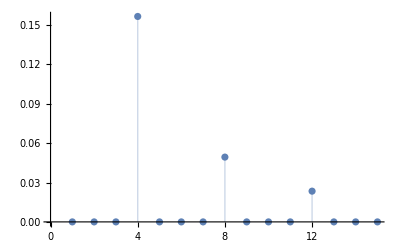
{76.1555,-Graphics-}

```mathematica
ListPlot[ParallelTable[{x,c2[x,4]},{x,1,15}], Filling->Axis] // AbsoluteTiming
```

```mathematica
Clear[q, Equation];
q[x_,k_, n_] := Integrate[Sec[θ-2*π*i/n-π/n]Cos[k*θ],θ]/.θ->x
q[2*π*(i+1)/4, 3, 4]-q[2*π*(i)/4,3,4]
```

(-1/2+ⅈ/2) (-1)^(1/4) (Cos[(3 i π)/2]+1/2 i π Cos[(3 i π)/2]+Sin[(3 i π)/2]+1/2 i π Sin[(3 i π)/2])+(1/2-ⅈ/2) (-1)^(1/4) (Cos[(i π)/2+(1+i) π]+Cos[(3 i π)/2] (1/2 (1+i) π-Log[Cos[(i π)/2-1/2 (1+i) π]-Sin[(i π)/2-1/2 (1+i) π]])+1/2 (1+i) π Sin[(3 i π)/2]+Log[Cos[(i π)/2-1/2 (1+i) π]-Sin[(i π)/2-1/2 (1+i) π]] Sin[(3 i π)/2]+Sin[(i π)/2+(1+i) π])

```mathematica
c2[n,k]
```

Integrate::idiv: Integral of Cos[n θ] Sec[(π+2 i π-k θ)/k] does not converge on {(2 i π)/k,(2 (1+i) π)/k}.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Sum`SumPolyTrigFunctionDump`it=Sum`SumPolyTrigFunctionDump`IteratedTrigSum[If[k>2,(ⅈ ⅇ^(-2 ⅈ Plus[«2»] Power[«2»] n π) (-Power[«2»] Plus[«2»] Hypergeometric2F1[«4»]+Power[«2»] Plus[«2»] Hypergeometric2F1[«4»]+Plus[«2»] Plus[«2»]))/(-1+Power[«2»]),Integrate[Cos[Collect[«2»]] Sec[Times[«2»]],{θ,2 i Power[«2»] π,2 Plus[«2»] Power[«2»] π},Assumptions→Or[«2»]&&Element[«2»]&&Element[«2»]&&And[«2»]&&And[«2»]]],{i,1}];RuleCondition[Sum`SumPolyTrigFunctionDump`it,Sum`SumPolyTrigFunctionDump`it=!=$Failed].

$Aborted

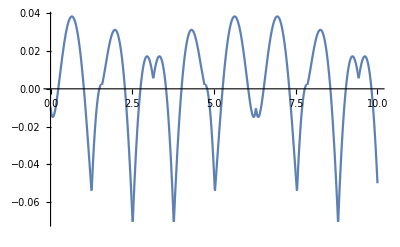

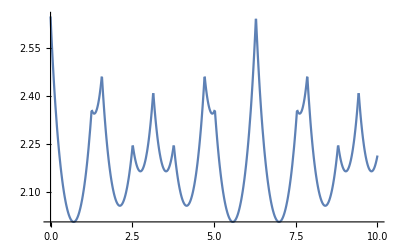

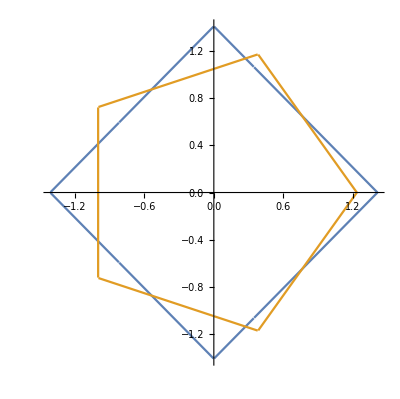

```mathematica
Plot[(r[θ, 4]-1.478)(r[θ, 5]-1.082), {θ, 0,10}]
Plot[(r[θ, 4])+(r[θ, 5]), {θ, 0,10}]
PolarPlot[{r[θ,4],r[θ,5]},{θ,0,2*π}]
```

```mathematica
N[Integrate[Sqrt[1+x^2],{x,-Tan[π/5],Tan[π/5]}]]/(2*Tan[π/5])
```

1.08206

```mathematica
Integrate[(r[θ, 4]-1.478)(r[θ, 5]-1.082),{θ,0,2*π}]
```

0.0200105+0. ⅈ

If the frequency of the wave is not a multiple of the n (for n-gon), then it will be off by some δ

```mathematica
Integrate[Sec[θ]Sin[θ+δ],{θ,-π/4,π/4}]
Plot[Sec[x],{x,0,10}]
```

The magnitude for each side with be:

```mathematica
1/2 π Sin[δ]
```

Summed across all sides it will be zero

```mathematica
π/2*Sum[Sin[2*π*i/k],{i, 0, k-1}]
```

0